# Problem 5

This problem is very similar to Chapter 8 - Problem 5. However, now we have an effective mass within the biased potential. Beware of this when building your transfer matrix!

Avocado and Mochi

#### Constants

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
mfe = 9.10938 * 10^-31; (* Mass of a free electron*)
e = 1.60217 * 10^-19;
ℏ = h/(2*Pi);
nano = 10^-9;
voltsPerNano = 1/nano;

α =Sqrt[(2*mfe*e)/ℏ^2];
Vext = 0.1;
Uext = -0.1;
```

#### Given information and wave numbers

We will split this problem into three regions:
Region 1 - The region to the left of the well (free space)
Region 2 - The region inside the well with an external bias
Region 3 - The region to the right of the well

```mathematica
mwell = 0.067 * mfe; (* Effective mass of the electron inside the well *)
L= 2*nano;
F = Vext/L;
k1 = α*Sqrt[en] ;
k3 = α*Sqrt[en-Uext] ;
Vo = -1;
```

```mathematica
zp[z_] = ((2*mwell)/ℏ^2)^(1/3)*(((Vo - en)*e)/(e*F)^(2/3) - (e*F)^(1/3)*z);
z0 = zp[0];
zL = zp[L];
zprime = D[zp[z],z];
```

#### From Region 1 to Region 2

From free space to biased potential
Wave equation in free space is e^ikz+e^-ikz
Wave equation in the biased potential is Ai(zp(z)) + Bi(zp(z))
The second equation was given in Professor Manassah’s Notes.

The boundary conditions states that at z = 0, the wave equations and their derivatives must be equal.
To build the following matrices, we just evaluate these wave equations and their derivatives at 0.

```mathematica
region1 = {{1,1},1/mfe*{I*k1, -I*k1}};
region20 = {{AiryAi[z0], AiryBi[z0]}, 1/mwell*{zprime*AiryAiPrime[z0], zprime*AiryBiPrime[z0]}};
transfer12 = Inverse[region1].region20;
```

#### From Region 2 to Region 3

Now the boundary conditions state that at L, the wave equations must be equal again.
The wave equation in Region 3 is almost the same as the one in Region 1, however we have to use a different wave number.

```mathematica
region2L = {{AiryAi[zL], AiryBi[zL]}, 1/mwell*{zprime*AiryAiPrime[zL], zprime*AiryBiPrime[zL]}};
region3 = {{Exp[I*k3*L], Exp[-I*k3*L]},1/mfe*{I*k3*Exp[I*k3*L], -I*k3*Exp[-I*k3*L]}};
transfer23 = Inverse[region2L].region3 ;
```

#### The Full transfer matrix of the electron

```mathematica
fullTransferMatrix = transfer12.transfer23;
```

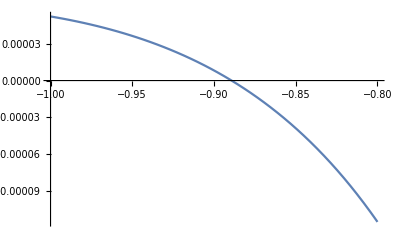

```mathematica
Plot[fullTransferMatrix[[1,1]],{en,-1,-0.8}]
```

```mathematica
FindRoot[fullTransferMatrix[[1,1]]==0, {en,-0.89}]
```

{en→-0.889253+0. ⅈ}